```mathematica
ClearAll["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
MyExportPDF[file_,figure_]:= Module[{outlinedGraphics},
outlinedGraphics=First@ImportString[ExportString[figure,"PDF"],"PDF","TextMode"->"Outlines"];
Export[file,outlinedGraphics];
]

Get["jlabColors`"]
Get["boxPlot`"]
Get["Spec743`"]
ColorSetter /@ jlabColorTable 

BRRad = 10; 
Bscatter = 50; 
Bxst = 1; 
Bxw = 100; 
Binc = 0; 
Bstep = 230; 
PrL = 400; 
PrH = 3300;
```

{0.7529411764705882,0.9764705882352941,0.1843137254901961,0.2549019607843137,0.8980392156862745,0.5019607843137255,0.49019607843137253}

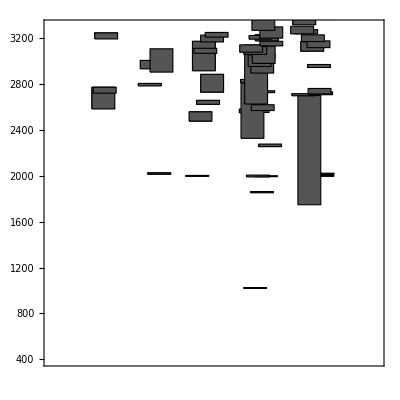

```mathematica
RRad = BRRad; 
scatter = Bscatter; 
xst = Bxst; 
xw = Bxw; 
inc = Binc; 
step = Bstep; 

A1mP = boxStack[ PA1mP[RRad,scatter,xst+inc*step,xw] ];++inc; 
A2mP = boxStack[ PA2mP[RRad,scatter,xst+inc*step,xw] ];++inc; 
EmP = boxStack[ PEmP[RRad,scatter,xst+inc*step,xw] ];++inc; 
T1mP = boxStack[ PT1mP[RRad,scatter,xst+inc*step,xw] ];++inc; 
T2mP = boxStack[ PT2mP[RRad,scatter,xst+inc*step,xw] ];++inc; 

ThePlotmP = Show[ A1mP , A2mP,EmP,T1mP,T2mP,
	PlotRange->{{xst- step,xst + inc*step+scatter}, {PrL,PrH}}, 
	Axes->False,
	Frame->{{True,True},{False,False}},
	FrameTicks->{{All,All},{None,None}},
	AspectRatio->1];
Magnify[ ThePlotmP, 4]
(*MyExportPDF[ "BoxPlotUnlabeledmP.pdf" , ThePlotmP ]*)
```

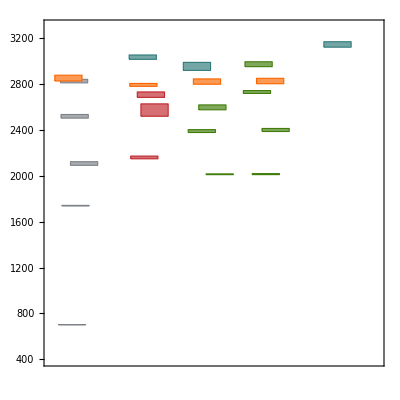

```mathematica
RRad = BRRad; 
scatter = Bscatter; 
xst = Bxst; 
xw = Bxw; 
inc = Binc; 
step = Bstep; 

A1mM = boxStack[ PA1mM[RRad,scatter,xst+inc*step,xw] ];++inc; 
T1mM = boxStack[ PT1mM[RRad,scatter,xst+inc*step,xw] ];++inc; 
T2mM = boxStack[ PT2mM[RRad,scatter,xst+inc*step,xw] ];++inc; 
EmM = boxStack[ PEmM[RRad,scatter,xst+inc*step,xw] ];++inc; 
A2mM = boxStack[ PA2mM[RRad,scatter,xst+inc*step,xw] ];++inc; 



ThePlotmM = Show[ A1mM,T1mM,T2mM,EmM, A2mM,
	PlotRange->{{xst- 0.5*step,xst + (inc-0.5)*step+scatter}, {PrL,PrH}}, 
	Axes->False,
	Frame->{{True,True},{False,False}},
	FrameTicks->{{All,All},{None,None}},
	AspectRatio->1];
Magnify[ ThePlotmM, 4]
MyExportPDF[ "BoxPlotUnlabeledmM.pdf" , ThePlotmM ]
```

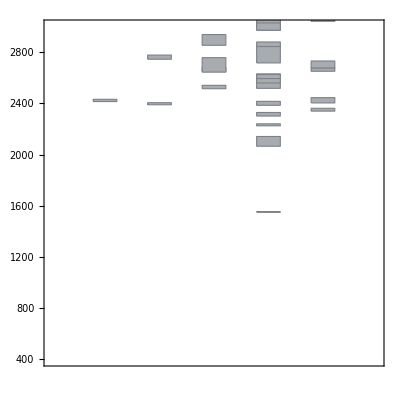

```mathematica
RRad = BRRad; 
scatter = Bscatter; 
xst = Bxst; 
xw = Bxw; 
inc = Binc; 
step = Bstep; 

A1pP = boxStack[ PA1pP[RRad,scatter,xst+inc*step,xw] ];++inc; 
A2pP = boxStack[ PA2pP[RRad,scatter,xst+inc*step,xw] ];++inc; 
EpP = boxStack[ PEpP[RRad,scatter,xst+inc*step,xw] ];++inc; 
T1pP = boxStack[ PT1pP[RRad,scatter,xst+inc*step,xw] ];++inc; 
T2pP = boxStack[ PT2pP[RRad,scatter,xst+inc*step,xw] ];++inc; 

ThePlotpP = Show[ A1pP , A2pP,EpP,T1pP,T2pP,
	PlotRange->{{xst- step,xst + inc*step+scatter},{PrL,PrH}}, 
	Axes->False,
	Frame->{{True,True},{False,False}},
	FrameTicks->{{All,All},{None,None}},
	AspectRatio->1];
Magnify[ ThePlotpP, 4]
MyExportPDF[ "BoxPlotUnlabeledpP.pdf" , ThePlotpP ]
```

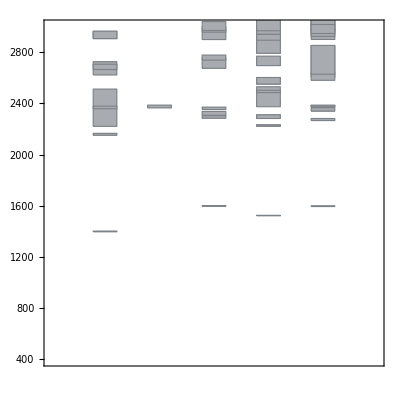

```mathematica
RRad = BRRad; 
scatter = Bscatter; 
xst = Bxst; 
xw = Bxw; 
inc = Binc; 
step = Bstep; 

A1pM = boxStack[ PA1pM[RRad,scatter,xst+inc*step,xw] ];++inc; 
A2pM = boxStack[ PA2pM[RRad,scatter,xst+inc*step,xw] ];++inc; 
EpM = boxStack[ PEpM[RRad,scatter,xst+inc*step,xw] ];++inc; 
T1pM = boxStack[ PT1pM[RRad,scatter,xst+inc*step,xw] ];++inc; 
T2pM = boxStack[ PT2pM[RRad,scatter,xst+inc*step,xw] ];++inc; 

ThePlotpM = Show[ A1pM, A2pM,EpM,T1pM,T2pM,
	PlotRange->{{xst- step,xst + inc*step+scatter}, {PrL,PrH}}, 
	Axes->False,
	Frame->{{True,True},{False,False}},
	FrameTicks->{{All,All},{None,None}},
	AspectRatio->1];
Magnify[ ThePlotpM, 4]
MyExportPDF[ "BoxPlotUnlabeledpM.pdf" , ThePlotpM ]
```